Complete The Wolfram Expression

Baschieri Daniele

Di Virgilio Riccardo

University of Bologna.

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: Design an interactive browser game where you can improve your skill with wolfram language, starting from a topic of your interest the system will show you a Wolfram Expression with a missing part to complete, in a growing of difficulty and fun.

SUMMARY OF WORK: Developing a web application based on Wolfram’s stack technology, focusing on exploring safe examples for the game in a dynamic self configuring context.
Application is ready for a public deployment, but with such a vast number of example more test are required to verify the stability of this alpha release.

RESULTS AND FUTURE  WORK: Application is now available in alpha stage on this link https://wolfr.am/complete-the-function the very next step is the releasing it on the WolframCloud and let it available for everyone. The gamification aspect of the application is really minimal right now, in the future could be useful add badges and karma-point in order to increase the fun and also adding multiple choice in the easy mode in order to balance the difficulty.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

The game is fully developed in Wolfram Mathematica Language, is composed with 3 different component:
The URLDispatcher redirect each http request on the correspondent template, it’s the entry point of the game and the most important part of the application.

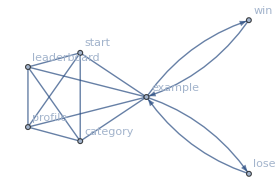

Current graph of the web page that URLDispatcher manage to present.

The second most important aspect of the game is the function that tweak a working wolfram expression and replace a Symbol with a Placeholder. (  1  )

```mathematica
Table[PieChart[{1,2,3},SectorOrigin->θ],{θ,{0,π/4,π/2}}]
```

```mathematica
Table[1[{1,2,3},SectorOrigin->θ],{θ,{0,π/4,π/2}}]
```

During this process is important to pay attention that the expression not evaluate, some Head like Now can produce different output if are not manage correctly.
Finally another section of this project is related with the classification of the exercise and the realization of a subset of instruction that can be used during the game.
Some Expression can be really dangerous for Wolfram Kernel. Expressions like Quit or Import, Export can compromise the Wolfram’s account of the user, so the system is designed to accept only a huge subset of expression and will present only the example form the documentation that contain expression in that’s safe subset.

-Graphics-

The best way to understand better the system is trying it at https://wolfr.am/complete-the-function

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Code

Provide one of:

Link to the GitHub

Explicit code

Written Content / Lesson Plans

Conclusions in Detail

All Visualizations

Data Sources Links/References

Future Directions

Background Info Links/References

Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```